```mathematica
Clear["Global`*"]
$PlotTheme="Scientific";
PositivePart[x_]:=If[x>=0,x,0];
R = {x, y, z};
$Assumptions = x ∈ Reals && y ∈ Reals && z ∈ Reals && ρ ∈ Reals && ρ > 0 && θ ∈ Reals && ϕ ∈ Reals && k ∈ Reals && k > 0 && ω > 0;
r = Sqrt[R . R];
k=ω;
predecessor[α_] := If[α == {0, 0, 0},
   {0, 0, 0},
   Select[
     Table[α - UnitVector[3, j], {j, 1, 3}],
     NonNegative@Min@# &,
     1
     ][[1]]
   ];
firstNonzeroDim[α_] := Position[
     α,
     _?(# > 0 &),
     Infinity, 1
     ][[1]][[1]];
g[α_,direction_] :=If[α[[1]]<α[[2]],
g[{α[[2]],α[[1]],α[[3]]},direction]/.x->y1/.y->x/.y1->y,
 If[α == {0, 0, 0},
1/4/π/r,
Block[{j, α1, ga},
α1 = α;
j = firstNonzeroDim[α];
α1[[j]] = α1[[j]] - 1;
ga = g[α1,direction];
D[ga, R[[j]]] -direction ⅉ k R[[j]]/r ga //Expand
]
]
]
h[α_,direction_] :=g[α,direction];
SimplifiedHeaviside[x_] := If[x >= 0, 1, 0];
SafeMoment[CurrentMoment_,α_,dim_]:=If[AllTrue[α,#>=0&],
CurrentMoment[α,dim],
0];
ChargeMoment[α_, CurrentMoment_, dim_,direction_] := -1/(direction ⅉ ω) Sum[If[dim == j,
    α[[j]] SimplifiedHeaviside[α[[j]] - 2] (α[[j]] - 1) SafeMoment[CurrentMoment,(α[[j]] - 2) UnitVector[3, j] +Total[ α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {j }]], j],
    α[[j]] α[[dim]] SimplifiedHeaviside[α[[j]] - 1] SimplifiedHeaviside[α[[dim]] - 1] SafeMoment[CurrentMoment,(α[[j]] - 1) UnitVector[3, j] + (α[[dim]] - 1) UnitVector[3, dim] + Total[α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {dim, j}]], j]
    ],
   {j, 1, 3}]
ElectricMoment[α_, CurrentMoment_, dim_,direction_] :=direction ⅉ ω CurrentMoment[α, dim] +ChargeMoment[α, CurrentMoment, dim,direction]
MagneticMoment[α_,CurrentMoment_, dim_,direction_] := -direction Sum[LeviCivitaTensor[3][[dim]][[i]][[j]] SimplifiedHeaviside[α[[i]] - 1] α[[i]] CurrentMoment[(α[[i]] - 1) UnitVector[3, i] +Total[ α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {i}]], j],
   {i, 1, 3}, {j, 1, 3}]
Field[α_, CurrentMoment_, MomentFunction_, dim_,direction_] := Block[{β},
β=(-1)^Norm[α, 1]/(Times @@ (Factorial/@ α)) MomentFunction[α, CurrentMoment, dim,direction];
If[β===0||β===0.,
0,
β h[α,direction]
]
]
ElectricField[α_, CurrentMoment_, dim_,direction_] := Field[α, CurrentMoment, ElectricMoment, dim,direction];
MagneticField[α_, CurrentMoment_, dim_,direction_] := Field[α, CurrentMoment, MagneticMoment, dim,direction];
On[Assert]
CurrentMoment[α_, dim_] := If[α == {0, 0, 0} && dim == 3,
  ⅉ ω p, 0]
EfieldThis = Simplify@TransformedField["Cartesian" -> "Spherical", Table[Sum[ElectricField[{ax, ay, az}, CurrentMoment, dim,-1],
      {ax, 0, 2}, {ay, 0, 2 - ax}, {az, 0, 2 - ax - ay}],
     {dim, 1, 3}], R -> {ρ, θ, ϕ}];
BfieldThis = Simplify@TransformedField["Cartesian" -> "Spherical", Table[Sum[MagneticField[{ax, ay, az}, CurrentMoment, dim,-1],
      {ax, 0, 2}, {ay, 0, 2 - ax}, {az, 0, 2 - ax - ay}],
     {dim, 1, 3}], R -> {ρ, θ, ϕ}];
P = {0, 0, p};
n = R/r;
HJackson = TransformedField["Cartesian" -> "Spherical",
    k^2/4/π n×P/r (1 - 1/ⅉ/k/r),
    R -> {ρ, θ, ϕ}]// Simplify;
EJackson = TransformedField["Cartesian" -> "Spherical",
    1/4/π (k^2/r (n×P)×n + (3 n (n . P) - P) (1/r^3 - ⅉ k/r^2)),
    R -> {ρ, θ, ϕ}] // Simplify;
Assert[Simplify[BfieldThis - HJackson] == {0, 0, 0}]
Assert[Simplify[EfieldThis - EJackson] == {0, 0, 0}]
Clear[CurrentMoment, EfieldThis, BfieldThis, P, n, HJackson, EJackson]
```

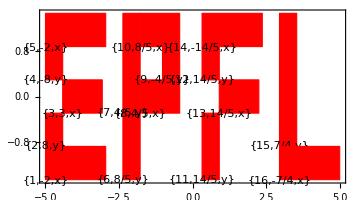

```mathematica
dirName=ToString@NotebookDirectory[];
a=5;
length=2a;
x1s={(*E*)0,0,10,0,0,(*P*)45,45,55,68,55,(*F*)91,91,101,91,(*L*)136,136};
x2s={(*E*)0,10,20,30,40,(*P*)0,20,20,30,40,(*F*)0,30,20,40,(*L*)10,0};
ws={(*E*)35,10,23,10,35,(*P*)10,10,23,10,23,(*F*)10,10,23,35,(*L*)10,35};
hs={(*E*)10,10,10,10,10,(*P*)20,30,10,10,10,(*F*)20,10,10,10,(*L*)40,10};
amplitudes={-2,8,6/2,-8,-2,(*P*)8/5,4/5,4/5,-4/5,8/5,(*F*)14/5,14/5,14/5,-14/5,(*L*)7/4,-7/4};
polarities={1,2,1,2,1,(*P*)2,2,1,2,1,(*F*)2,2,1,1,(*L*)2,1};
d1 = a;
lengthLogo = 171;

(*d1=a/5;
slice=;;5;
x1s=x1s[[slice]];
x2s=x2s[[slice]];
ws=ws[[slice]];
hs=hs[[slice]];
amplitudes=amplitudes[[slice]];
polarities=polarities[[slice]];*)

d2 = a * 50 / lengthLogo;
Graphics[Flatten@
MapThread[
{{EdgeForm[Thin],Red,Rectangle[{#1,#2},{#1+#3,#2+#4}]},
{Black,Text[{#5,#6,{x,y}[[#7]]},{#1,#2}]}
}&
,{x1s/lengthLogo length-d1,x2s/lengthLogo length-d2,ws/lengthLogo length,hs/lengthLogo length,Range[Length@x1s],amplitudes,polarities}],
ImageSize->Medium,
Frame->True
]
IntJ=Function[{x0,σ,m},
1/(m+1)((x0+σ/2)^(m+1)-(x0-σ/2)^(m+1))
];
CJ=Function[{α,x1,x2,w,h},
IntJ[x1+w/2,w,α[[1]]]IntJ[x2+h/2,h,α[[2]]]
];
Clear[CurrentMoment];
CurrentMoment[α_,dim_]:=CurrentMoment[α,dim]=If[α[[3]]==0,
ⅈ ω Sum[
If[polarities[[i]]==dim,
CJ[α,x1s[[i]]/lengthLogo length-d1,x2s[[i]]/lengthLogo length-d2,ws[[i]]/lengthLogo length,hs[[i]]/lengthLogo length]amplitudes[[i]],
0],
{i,1,Length@x1s}],
0];
maxOrder=120;
```

```mathematica
rz=Sqrt[x^2+y^2];
antiderivative=Integrate[Exp[-t^2],t];
derivatives=Association@Table[
{i-1,dir}->Expand[FunctionExpand[
D[antiderivative,{t,i}]
]/.t->-dir rz],
{i,0,maxOrder+3},{dir,-1,1,2}];
Table[CurrentMoment[{ax,ay,0},dim],
{ax,0,maxOrder},{ay,0,maxOrder-ax},{dim,1,2}];
(*Table[Monitor[g[{ax,ay,0},direction],{ax,ay,direction}];,
{ax,0,maxOrder},{ay,0,maxOrder-ax},{direction,-1,1,2}];
DumpSave[dirName<>"data/g-up-to-order-"<>ToString@maxOrder<>".mx",g];*)
```

```mathematica
Efield=0;
```

```mathematica
knownOrder=85;
Efield=Import[dirName<>"data/field-v3-order-"<>ToString@knownOrder<>"-a-"<>ToString@a<>".mx"];
```

```mathematica
d=Table[Monitor[
Efield+=#1+#2&@@Table[
Table[
Sum[
Total@MapIndexed[{expr,index}↦expr derivatives[{index[[1]]-2,direction}]/(ⅈ)^(index[[1]]-1),
CoefficientList[
ElectricField[{ax,order-ax,0},CurrentMoment,dim,direction]/.z->0,ω]],
{ax,0,order}],
{dim,1,2}
],{direction,-1,1,2}
];
Efield=Expand@Efield;
Export[
dirName<>"data/field-v3-order-"<>ToString[order]<>"-a-"<>ToString[a]<>".mx",
Efield
],
order]//AbsoluteTiming,{order,knownOrder+1,maxOrder}
]
```

$Aborted

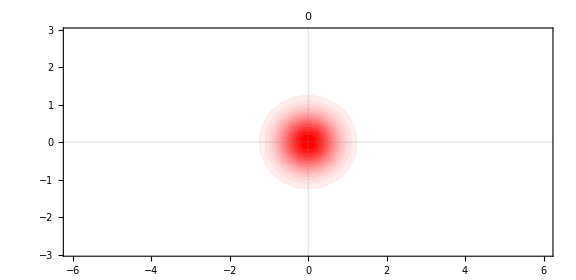
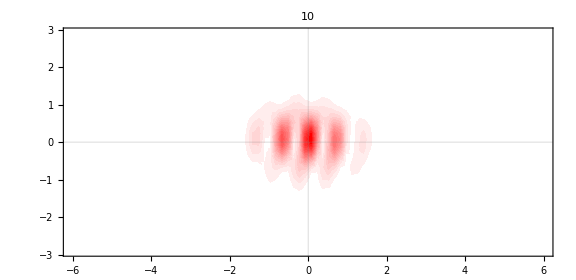
{/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza/data/plot-order-0-a-5.pdf -Graphics-,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza/data/plot-order-10-a-5.pdf -Graphics-}

```mathematica
Table[
Monitor[
Block[{imported,x,y,z},
imported=Import[ToString@NotebookDirectory[]<>"data/v3-order-"<>ToString[order]<>"-a-"<>ToString@a<>".mx"];
x=imported["x"];
y=imported["y"];
z=imported["discrete norm"];
plot=ListContourPlot[
Flatten[
Table[
{x[[i]],y[[j]],z[[i,j]]},
{i,1,Length@x},{j,1,Length@y}],1],
PlotRange->Full,
PlotLabel->order,
AspectRatio->Max@y/Max@x,
ColorFunction->(Blend[{White,Red},#1]&),
ImageSize->Large,
Contours->20,
ContourStyle->None,
PlotLegends->None
]
Export[dirName<>"data/plot-order-"<>ToString@order<>"-a-"<>ToString@a<>".pdf",plot]
],order],
{order,0,10,10}
]
```

```mathematica
Table[Monitor[
Efield=Import[ToString@NotebookDirectory[]<>"data/field-v3-order-"<>ToString[order]<>"-a-"<>ToString[a]<>".mx"];
norm=Total[Efield^2];
plotLimitX=6/5a;plotLimitY=2a 50/171;nPointsX=81;nPointsY=Round[nPointsX plotLimitY/plotLimitX];xd=Subdivide[-plotLimitX,plotLimitX,nPointsX];yd=Subdivide[-plotLimitY,plotLimitY,nPointsY];normd=Table[
N[norm/.x->xd[[i]]/.y->yd[[j]],50],
{i,1,Length@xd},{j,1,Length@yd}];
Export[ToString@NotebookDirectory[]<>"data/v3-order-"<>ToString[order]<>"-a-"<>ToString[a]<>".mx",
<|"x"->xd,"y"->yd,"discrete norm"->normd|>],
order],{order,20,80,10}]
```